```mathematica
<<"C:\\Users\\dclu1\\Google 云端硬盘\\Proj\\toolkit\\toolkit.m"
```

## NCM Algebra

### General functions

```mathematica
(*a[__] to represent fermion/boson operator, d/o represent dagger or not*)
expandNCM[(h:NonCommutativeMultiply)[a___,b_Plus,c___]]:=Distribute[h[a,b,c],Plus,h,Plus,expandNCM[h[##]]&]
expandNCM[(h:NonCommutativeMultiply)[a___,b_Times,c___]]:=Most[b]expandNCM[h[a,Last[b],c]]
expandNCM[a_]:=ExpandAll[a]
ExpandNCM[exp_]:=Block[{exp1},
exp1=expandNCM[exp];
Distribute[fggsfsf[exp1]]/.fggsfsf->expandNCM
]
(*g acts on coefficients, f acts on NonCM*)
sendNCM[(h:Times)[a___,b_NonCommutativeMultiply],g_,f_]:=g[Times[a]]f[b]
sendNCM[b_NonCommutativeMultiply,g_,f_]:=f[b]
sendNCM[(h:Times)[a___,c[k___]],g_,f_]:=g[Times[a]]f[c[k]]
sendNCM[c[k___],g_,f_]:=f[c[k]]
sendNCM[(h:Times)[tt___,a[k___]],g_,f_]:=g[Times[tt]]f[a[k]]
sendNCM[a[k___],g_,f_]:=f[a[k]]

AppToNCM[exp_,g_,f_]:=Distribute[sendNCM[ExpandNCM[exp],g,f]]
takeDag[exp_]:=AppToNCM[exp,Conjugate,Reverse]/.{d->o,o->d}
```

##### check

```mathematica
OrderedQ[{d,o}]
```

True

```mathematica
a[•,1]
```

a[•,1]

```mathematica
exp1=(a[d,1,j,k]**a[o,3,i,j]+a[d,2,i,o])**a[d,i,a,l]
```

(a[d,2,i,o]+a[d,1,j,k]**a[o,3,i,j])**a[d,i,a,l]

```mathematica
AppToNCM[exp1,Identity,Reverse]
```

a[d,i,a,l]**a[d,2,i,o]+a[d,i,a,l]**a[o,3,i,j]**a[d,1,j,k]

```mathematica
Reverse[p1**p2**p3]
```

p3**p2**p1

```mathematica
Head[exp1]
```

NonCommutativeMultiply

```mathematica
Head[a**b+c**d]
```

Plus

### Bosonization dict

We use a[_,_,_] to represent fermion operator ψ, [l/r,s/x,d/o] → L/R, ↑/↓, †/-

```mathematica
p={a[l,s,o],a[l,x,o],a[r,s,o],a[r,x,o]};
pd={a[l,s,d],a[l,x,d],a[r,s,d],a[r,x,d]};
pl=p⟦1;;2⟧;
pr=p⟦3;;4⟧;
pld=pd⟦1;;2⟧;
prd=pd⟦3;;4⟧;
```

```mathematica
term[l_,v_,r_]:=Sum[v⟦i,j⟧l⟦i⟧**r⟦j⟧,{i,Length@v},{j,Length@v}]
takeDag[exp_]:=AppToNCM[exp,Conjugate,Reverse]/.{d->o,o->d}
```

because of the point split, we don’t have delta function, we would like to convert the operator expression in the order of their labels, namely,

ψ_(L↑)^(d/o)ψ_(L↓)^(d/o)ψ_(R↑)^(d/o)ψ_(R↓)^(d/o)

```mathematica
NOBosonization[0]=0;
NOBosonization[left___,a_[k1__],b_[k2__],right___]/;!OrderedQ[{{k1},{k2}}]:=-NOBosonization[left,b[k2],a[k1],right];
NOrderBosonization[exp_]:=AppToNCM[exp,Identity,NOBosonization]/.{NonCommutativeMultiply[ss__]:> ss}

(*Representation*)
rules={a[l,s,d]->"ψ_(L↑)^†",a[l,s,o]->"ψ_(L↑)",a[l,x,d]->"ψ_(L↓)^†",
a[l,x,o]->"ψ_(L↓)",a[r,s,d]->"ψ_(R↑)^†",a[r,s,o]->"ψ_(R↑)",
a[r,x,d]->"ψ_(R↓)^†",a[r,x,o]->"ψ_(R↓)",
a[d]->"ψ^†",a[o]->"ψ"};

represent[exp_]:=(exp/.NOBosonization[a__]:>NO[a])/.rules
```

```mathematica
NOrderBosonization[term[pd,σs[1,2],p]**term[pd,σs[2,3],p]]//represent
```

NO[ψ_(L↓),ψ_(L↓),ψ_(R↑)^†,ψ_(R↓)^†]-NO[ψ_(L↑),ψ_(L↓),ψ_(R↓)^†,ψ_(R↓)^†]+NO[ψ_(L↑),ψ_(L↓),ψ_(R↑)^†,ψ_(R↑)^†]-NO[ψ_(L↑),ψ_(L↑),ψ_(R↑)^†,ψ_(R↓)^†]-NO[ψ_(L↑),ψ_(L↓)^†,ψ_(R↓)^†,ψ_(R↓)]-NO[ψ_(L↑),ψ_(L↓)^†,ψ_(R↑)^†,ψ_(R↑)]+NO[ψ_(L↓)^†,ψ_(L↓),ψ_(R↑),ψ_(R↓)^†]-NO[ψ_(L↓)^†,ψ_(L↓),ψ_(R↑)^†,ψ_(R↓)]+NO[ψ_(L↓)^†,ψ_(L↓)^†,ψ_(R↑),ψ_(R↓)]+NO[ψ_(L↑)^†,ψ_(L↓),ψ_(R↓)^†,ψ_(R↓)]+NO[ψ_(L↑)^†,ψ_(L↓),ψ_(R↑)^†,ψ_(R↑)]+NO[ψ_(L↑)^†,ψ_(L↑),ψ_(R↑),ψ_(R↓)^†]-NO[ψ_(L↑)^†,ψ_(L↑),ψ_(R↑)^†,ψ_(R↓)]-NO[ψ_(L↑)^†,ψ_(L↓)^†,ψ_(R↓),ψ_(R↓)]+NO[ψ_(L↑)^†,ψ_(L↓)^†,ψ_(R↑),ψ_(R↑)]-NO[ψ_(L↑)^†,ψ_(L↑)^†,ψ_(R↑),ψ_(R↓)]

### Fermion/Boson Normal Ordering

```mathematica
(*
NOrderB::usage="[NCM] gives boson normal ordering, a[d,...] a[o,...] reps creation/annihilation"
NOrderF::usage="[NCM] gives fermion normal ordering, c[d,...] c[o,...] reps creation/annihilation"
WickCon::usage="[exp,NOrderB/F] wick contraction"
norderB::usage="boson normal ordering"
norderF::usage="boson normal ordering"
*)
```

we would like to move all the creation operators to the left and annihilation operators to the right, the operators are represented as,

ψ_(αβγδ...)^(†/o)=a[d/o,α,β,γ,δ,...]

[a_k1,a_k2^†]=δ_(k1,k2) ⇒ a_k1 a_k1^†=1+a_k1^†a_k1;   a_k1 a_k2^†=a_k2^†a_k1
a_k1 a_k2=a_k2 a_k1;   a_k1^†a_k2^†=a_k2^†a_k1^†
a_k1^†a_k1=n_k1

```mathematica
ClearAll[norderB,NOrderB]
norderB[]=1;
(*Commutation relation:[a(k1),a†(k2)]=δ(k1,k2) *)
norderB[left___,a[o,k1__],a[d,k2__],right___]:=
norderB[left,a[d,k2],a[o,k1],right]+Times@@MapThread[δ,{{k1},{k2}}]norderB[left,right];

(*Commutation relations:[a(k1),a(k2)]=[a†(k1),a†(k2)]=0*)
norderB[left___,a[o,k1__],a[o,k2__],right___]/;!OrderedQ[{{k1},{k2}}]:=norderB[left,a[o,k2],a[o,k1],right];
norderB[left___,a[d,k1__],a[d,k2__],right___]/;!OrderedQ[{{k1},{k2}}]:=norderB[left,a[d,k2],a[d,k1],right];

NOrderB[exp_]:=AppToNCM[exp,Identity,norderB]/.{NonCommutativeMultiply[ss__]:> ss}
```

{a_k1,a_k2^†}=δ_(k1,k2) ⇒ a_k1 a_k2^†=δ_(k1,k2)-a_k2^†a_k1;   a_k1 a_k2^†=-a_k2^†a_k1
a_k1 a_k2=-a_k2 a_k1;   a_k1^†a_k2^†=-a_k2^†a_k1^†
a_k1^†a_k1=n_k1

```mathematica
(*Now for fermion!!*)
ClearAll[norderF,NOrderF]
norderF[]=1;
(*Commutation relation:{c(k1),c†(k2)}=δ(k1,k2) *)
norderF[left___,c[o,k1__],c[d,k2__],right___]:=
-norderF[left,c[d,k2],c[o,k1],right]+Times@@MapThread[δ,{{k1},{k2}}]norderF[left,right];

(*Commutation relations:{c(k1),c(k2)}={c†(k1),c†(k2)}=0*)
norderF[left___,c[o,k1__],c[o,k2__],right___]/;!OrderedQ[{{k1},{k2}}]:=-norderF[left,c[o,k2],c[o,k1],right];
norderF[left___,c[d,k1__],c[d,k2__],right___]/;!OrderedQ[{{k1},{k2}}]:=-norderF[left,c[d,k2],c[d,k1],right];

NOrderF[exp_]:=AppToNCM[exp,Identity,norderF]/.{NonCommutativeMultiply[ss__]:> ss}
```

```mathematica
NCMAntiCommutator[a_,b_]:=a**b+b**a
NCMCommutator[a_,b_]:=a**b-b**a
```

wick contraction

```mathematica
wickcon[___,_[o,__]]:=0;
wickcon[_[d,__],___]:=0;
WickCon[exp_,f_]:=f[exp]/.{norderB->wickcon,norderF->wickcon}
```

waste

```mathematica
ClearAll[wickconB,WickConB]
wickconB[]=1;
(*Commutation relation:[a(k1),a†(k2)]=δ(k1,k2) *)
wickconB[left___,a[o,k1__],a[d,k2__],right___]:=
wickconB[left,a[d,k2],a[o,k1],right]+Times@@MapThread[δ,{{k1},{k2}}]wickconB[left,right];


(*Commutation relations:[a(k1),a(k2)]=[a†(k1),a†(k2)]=0*)
wickconB[left___,a[o,k1__],a[o,k2__],right___]/;!OrderedQ[{{k1},{k2}}]:=wickconB[left,a[o,k2],a[o,k1],right];
wickconB[left___,a[d,k1__],a[d,k2__],right___]/;!OrderedQ[{{k1},{k2}}]:=wickconB[left,a[d,k2],a[d,k1],right];

wickconB[___,a[o,__]]:=0;
wickconB[a[d,__],___]:=0;

WickConB[exp_]:=AppToNCM[exp,Identity,wickconB]/.{NonCommutativeMultiply[ss__]:> ss}
```

```mathematica
ClearAll[wickconF,WickConF]
wickconF[]=1;
(*Commutation relation:{c(k1),c†(k2)}=δ(k1,k2) *)
wickconF[left___,c[o,k1__],c[d,k2__],right___]:=
-wickconF[left,c[d,k2],c[o,k1],right]+Times@@MapThread[δ,{{k1},{k2}}]wickconF[left,right];


(*Commutation relations:[a(k1),a(k2)]=[a†(k1),a†(k2)]=0*)
wickconF[left___,c[o,k1__],c[o,k2__],right___]/;!OrderedQ[{{k1},{k2}}]:=-wickconF[left,c[o,k2],c[o,k1],right];
wickconF[left___,c[d,k1__],c[d,k2__],right___]/;!OrderedQ[{{k1},{k2}}]:=-wickconF[left,a[d,k2],a[d,k1],right];

wickconF[___,c[o,__]]:=0;
wickconF[c[d,__],___]:=0;

WickConF[exp_]:=AppToNCM[exp,Identity,wickconF]/.{NonCommutativeMultiply[ss__]:> ss}
```

### Fourier transformation

```mathematica
Begin["cFourier"]
```

```mathematica
Clear[cfourier,cfourier1c,cfouriernc,cfourierExpand,generateKlist]
generateKlist[n_,l_]:=Block[{kk={kx,ky,kz,kw}},Array[ToExpression[ToString[kk⟦#2⟧]<>ToString[#1]]&,{n,l}]]
cfourier1c[c[o,i:{__},α___],k:{__}]:={c[o,k,α],ⅇ^(ⅈ k.i)}
cfourier1c[c[d,i:{__},α___],k:{__}]:={c[d,k,α],ⅇ^(-ⅈ k.i)}
cfouriernc[bbb_,dim_]:=Block[{exp},
exp=Thread@MapThread[cfourier1c,{{bbb},generateKlist[Length@{bbb},dim]}];
Times@@Flatten[exp]
]
cfouriernc[bbb__,dim_]:=Block[{exp},
exp=Thread@MapThread[cfourier1c,{{bbb},generateKlist[Length@{bbb},dim]}];
(Times@@exp⟦2⟧)NonCommutativeMultiply@@exp⟦1⟧
]
cfourier[exp_,dim_]:=Block[{exp1},
exp1=AppToNCM[exp,Identity,f[#,dim]&]/.NonCommutativeMultiply[ss__]:>ss;
exp1/.f-> cfouriernc
]


ClearAll[exponentExpand]
exponentExpand[(h:Power)[a_,b_],i:{___}]:=Block[{ilist},
ilist=CoefficientList[b,i];
If[Length@ilist<2,"No "<>ToString[i],
If[Length@i==1,a^ilist⟦1⟧exp[ilist⟦2⟧,i⟦1⟧],
If[Length@i==2,a^ilist⟦1,1⟧exp[{ilist⟦2,1⟧,ilist⟦1,2⟧},i],
If[Length@i==3,a^ilist⟦1,1,1⟧exp[{ilist⟦2,1,1⟧,ilist⟦1,2,1⟧,ilist⟦1,1,2⟧},i]]]]
]
]
exponentExpand[(h:Times)[a___],i:{__}]:=h@@(exponentExpand[#,i]&/@{a})
exponentExpand[a_,i_]:=a

cfourierExpand[exp_,i_]:=AppToNCM[exp,exponentExpand[#,i]&,Identity]

ClearAll[cSumss,cSum]
cSumss[(h:Power)[a_,b_],i:{___}]:=Block[{ilist},
ilist=CoefficientList[b,i];
If[Length@ilist<2,"No "<>ToString[i],
If[Length@i==1,a^ilist⟦1⟧Times@@(δ/@{ilist⟦2⟧}),
If[Length@i==2,a^ilist⟦1,1⟧Times@@(δ/@{ilist⟦2,1⟧,ilist⟦1,2⟧}),
If[Length@i==3,a^ilist⟦1,1,1⟧Times@@(δ/@{ilist⟦2,1,1⟧,ilist⟦1,2,1⟧,ilist⟦1,1,2⟧})]]]
]
]
cSumss[(h:Times)[a___],i:{__}]:=h@@(cSumss[#,i]&/@{a})
cSumss[a_,i_]:=a

cSum[exp_,i_]:=AppToNCM[exp,cSumss[#,i]&,Identity]
δ[0]:=1;
```

##### Chiral spin liquid

```mathematica
hk1=Block[{k,rx,ry,rμ,cij0,cijx,cijy,cijxy,ind,nn1,nn,hk,getData,ncmMatrix,χ1,χ2,χ3,χ4},
{χ1,χ2,χ3,χ4}={ⅈ,ⅈ,-ⅈ,ⅈ};
k={kx,ky};
rx={2,0};
ry={0,2};
rμ={{0,0},{0,1},{1,0},{1,1}};
ind=AssociationThread[{aa,bb,cc,dd},{1,2,3,4}];
cij0[a_,b_]:=c[d,{i,j}+rμ⟦ind[b]⟧,b]**c[o,{i,j}+rμ⟦ind[a]⟧,a];
cijx[a_,b_]:=c[d,{i,j}+rμ⟦ind[b]⟧+rx,b]**c[o,{i,j}+rμ⟦ind[a]⟧,a];
cijy[a_,b_]:=c[d,{i,j}+rμ⟦ind[b]⟧+ry,b]**c[o,{i,j}+rμ⟦ind[a]⟧,a];
cijxy[a_,b_]:=c[d,{i,j}+rμ⟦ind[b]⟧+rx+ry,b]**c[o,{i,j}+rμ⟦ind[a]⟧,a];
nn1=χ1 cij0[aa,cc]+χ2 cij0[cc,dd]+χ3 cij0[dd,bb]+χ4 cij0[bb,aa]+χ2 cijy[bb,aa]+Conjugate[χ4] cijy[dd,cc]+χ1 cijx[dd,bb]+Conjugate[χ3] cijx[cc,aa];
nn=nn1+takeDag[nn1];
hk=cSum[cfourier[nn,2],{i,j}]/.{kx2->kx1,ky2->ky1};

getData[c[d,{kx1,ky1},pp1__]**c[o,{kx1,ky1},pp2__]]:=ind/@{pp1,pp2};
ncmMatrix[(h:Times)[a___,b_NonCommutativeMultiply]]:=SparseArray[getData[b]->Times@a,{4,4}];
ExpToTrig[Distribute[ncmMatrix[hk]]]
];
hk1//MatrixForm
```

(0 | 2 ⅈ Cos[ky1] | -2 Sin[kx1] | 0
-2 ⅈ Cos[ky1] | 0 | 0 | -2 Sin[kx1]
-2 Sin[kx1] | 0 | 0 | -2 ⅈ Cos[ky1]
0 | -2 Sin[kx1] | 2 ⅈ Cos[ky1] | 0)

```mathematica
σfind[hk1]
```

-2 Conjugate[Sin[kx1]] σ^{1,0}-2 Conjugate[Cos[ky1]] σ^{3,2}

##### Graphene

```mathematica
Block[{k,δ1,δ2,δ3,hop1,hop,δ,hk},
k={kx,ky};
δ1={1,√3}/2;
δ2={1,-√3}/2;
δ3={-1,0};
(* Subscript[C, B]^†Subscript[C, A]+... *)
hop1=Sum[c[d,{i,j}+dμ,B]**c[o,{i,j},A],{dμ,{δ1,δ2,δ3}}];
hop=hop1+takeDag[hop1];
δ[0]:=1;
hk=((cSum[#,{i,j}]&@cfourier[hop,2])/.{kx2->kx1,ky2->ky1});
CoefficientList[hk,{c[d,{kx1,ky1},A]**c[o,{kx1,ky1},B],c[d,{kx1,ky1},B]**c[o,{kx1,ky1},A]}]
]
```

{{0,ⅇ^(-ⅈ kx1)+ⅇ^((ⅈ kx1)/2-1/2 ⅈ √3 ky1)+ⅇ^((ⅈ kx1)/2+1/2 ⅈ √3 ky1)},{ⅇ^(ⅈ kx1)+ⅇ^(-(ⅈ kx1)/2-1/2 ⅈ √3 ky1)+ⅇ^(-(ⅈ kx1)/2+1/2 ⅈ √3 ky1),0}}

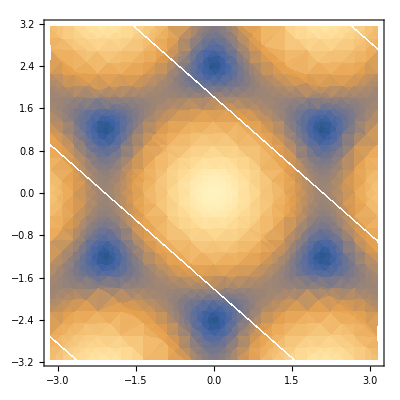

```mathematica
DensityPlot[Evaluate[Eigenvalues[{{0,ⅇ^(-ⅈ kx1)+ⅇ^((ⅈ kx1)/2-1/2 ⅈ √3 ky1)+ⅇ^((ⅈ kx1)/2+1/2 ⅈ √3 ky1)},{ⅇ^(ⅈ kx1)+ⅇ^(-(ⅈ kx1)/2-1/2 ⅈ √3 ky1)+ⅇ^(-(ⅈ kx1)/2+1/2 ⅈ √3 ky1),0}}]]⟦2⟧,{kx1,-π,π},{ky1,-π,π}]
```

```mathematica
Block[{h,hk},
h=(1-ϕ)c[d,{i},b]**c[o,{i+1},a]+(1+ϕ)c[d,{i+1},a]**c[o,{i+2},b];
h=h+takeDag[h];
hk=cSum[cfourier[h,1],{i}]/.kx2->kx1;
ind=AssociationThread[{a,b}->{1,2}];
getData[c[d,{kx1},pp1__]**c[o,{kx1},pp2__]]:=ind/@{pp1,pp2};
ncmMatrix[(h:Times)[a___,b_NonCommutativeMultiply]]:=SparseArray[getData[b]->Times@a,{2,2}];
Simplify[Distribute[ncmMatrix[hk]],Assumptions->{ϕ∈Reals}]//MatrixForm
]
```

(0 | ⅇ^(-ⅈ kx1) (1-ϕ+ⅇ^(2 ⅈ kx1) (1+ϕ))
ⅇ^(-ⅈ kx1) (1-ⅇ^(2 ⅈ kx1) (-1+ϕ)+ϕ) | 0)

```mathematica
Simplify@ExpToTrig[Normal@({{0, ⅇ^(-ⅈ kx1) (1-ϕ+ⅇ^(2 ⅈ kx1) (1+ϕ))}, {ⅇ^(-ⅈ kx1) (1-ⅇ^(2 ⅈ kx1) (-1+ϕ)+ϕ), 0}})]
```

{{0,2 (Cos[kx1]+ⅈ ϕ Sin[kx1])},{2 (Cos[kx1]-ⅈ ϕ Sin[kx1]),0}}

```mathematica
Simplify[Eigenvalues[{{0,2 (Cos[kx1]+ⅈ ϕ Sin[kx1])},{2 (Cos[kx1]-ⅈ ϕ Sin[kx1]),0}}],Assumptions->{ϕ∈Reals,ϕ<1}]
```

{-ⅈ √(-2 (1+ϕ^2)+2 (-1+ϕ^2) Cos[2 kx1]),ⅈ √(-2 (1+ϕ^2)+2 (-1+ϕ^2) Cos[2 kx1])}

```mathematica
Eigenvalues[{{0,a},{ac,0}}]
```

{-√a √ac,√a √ac}

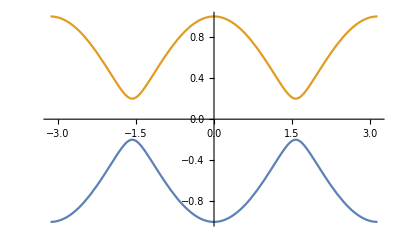

```mathematica
With[{ϕ=0.2},Plot[{-√(Cos[k]^2+ϕ^2 Sin[k]^2),√(Cos[k]^2+ϕ^2 Sin[k]^2)},{k,-π,π}]]
```

```mathematica
Series[√(Cos[k]^2+ϕ^2 Sin[k]^2),{k,π/2,2}]
```

√(ϕ^2)+((1-ϕ^2) (k-π/2)^2)/(2 √(ϕ^2))+O[k-π/2]^3